# Reunión del 22-08-2024

## Importando cosas

```mathematica
Get[NotebookDirectory[]<>"../AmadoTemp/DTQW.wl"]
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
<<MaTeX`
```

Get::noopen: Cannot open MaTeX`.

$Failed

## Definiendo variables

```mathematica
IndigoC=RGBColor["#729cfc"];
AquaC=RGBColor["#4bd7e5"];
DeepBlueC=RGBColor["#1e2c88"];
```

```mathematica
qlabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"../Mariana/Labels_pos.pdf","../Mariana/Labels_prob.pdf"};
clabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"../Mariana/Labels_pos.pdf","../Mariana/Labels_probc.pdf"};
plotargs={
BaseStyle->{FontFamily->"LM Roman 12",FontSize->15},
Axes->False,
Frame->True,
Mesh->All,
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,Opacity[0.5]]
};
```

```mathematica
TeXLabel[tlist_List]:=MaTeX[
"\\begin{gathered}\n"<>Fold[
StringJoin[#1,"\\\\\n",#2]&,ToString@StringForm["\\text{``}",#]&/@tlist
]<>"\n\\end{gathered}",
FontSize->14,
Magnification->1.3,
"Preamble"->{"\\usepackage{physics}"}
]
```

```mathematica
rowQW[state_,steps_]:=Module[
{rho,prob},
rho=#.#†&@DTQW2[state,steps];
prob=Abs@Diagonal@MatrixPartialTrace[rho,1,{2,201}]
]
QPascal[state_,steps_]:=Module[
{},
TableForm[#,
TableHeadings->{Range[0,steps],Ket[{#}]&/@ Range[-steps,steps]},
TableSpacing->{2, 2},
TableAlignments->Center,
Label
]&@
(rowQW[state,#][[101-steps;;101+steps]]&/@Range[0,steps])
]
```

```mathematica
(* Poner esto en el paquete *)
PascalRow[n_Integer]:=Riffle[Binomial[n,#]/(2^n)&@Range[0,n],0]
RandomWalkDistribution[n_Integer]:=Transpose[{Range[-n,n],PascalRow[n]}]
```

## Inicializaciones

```mathematica
InitializeDTQW[2,201]
MakeCoin[1/2,0,0];
MakeShift[];
MakeUnitary[];
```

## Resultados

## Estados puros de la moneda

### Estados 0,0

```mathematica
psi00=VectorState[{{1,0,0}}]
```

VectorState[{{1,0,0}}]

```mathematica
rhof00=#.#†&@DTQW2[psi00,100];
```

```mathematica
probs00=Abs@Diagonal@MatrixPartialTrace[rhof00,1,{2,201}];
```

```mathematica
Total@probs00
```

1.

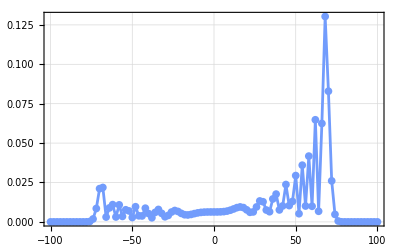

```mathematica
plot00=ListLinePlot[{Range[-100,100,2],probs00[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

### Estado 1,0

```mathematica
psi10=VectorState[{{1,1,0}}]
```

VectorState[{{1,1,0}}]

```mathematica
rhof10=#.#†&@DTQW2[psi10,100];
```

```mathematica
probs10=Abs@Diagonal@MatrixPartialTrace[rhof10,1,{2,201}];
```

```mathematica
Total@probs10
```

1.

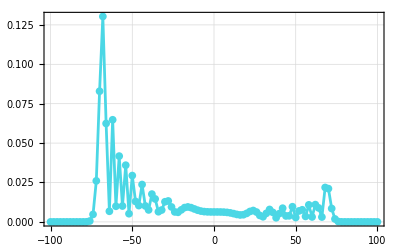

```mathematica
plot10=ListLinePlot[{Range[-100,100,2],probs10[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->AquaC
]
```

### Estado+_x,0

```mathematica
psiplusx0=VectorState[{{1/Sqrt[2],0,0},{1/Sqrt[2],1,0}}]
```

VectorState[{{1/(√2),0,0},{1/(√2),1,0}}]

```mathematica
rhofplusx0=#.#†&@DTQW2[psiplusx0,100];
```

```mathematica
probsplusx0=Abs@Diagonal@MatrixPartialTrace[rhofplusx0,1,{2,201}];
```

```mathematica
Total@probsplusx0
```

1.

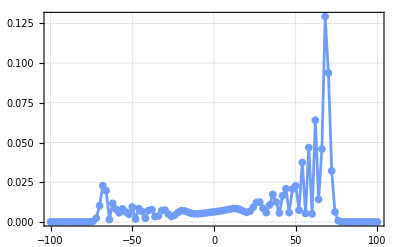

```mathematica
plotplusx0=ListLinePlot[{Range[-100,100,2],probsplusx0[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

### Estado -_x,0

```mathematica
psiminusx0=VectorState[{{1/Sqrt[2],0,0},{-1/Sqrt[2],1,0}}]
```

VectorState[{{1/(√2),0,0},{-1/(√2),1,0}}]

```mathematica
rhofminusx0=#.#†&@DTQW2[psiminusx0,100];
```

```mathematica
probsminusx0=Abs@Diagonal@MatrixPartialTrace[rhofminusx0,1,{2,201}];
```

```mathematica
Total@probsminusx0
```

1.

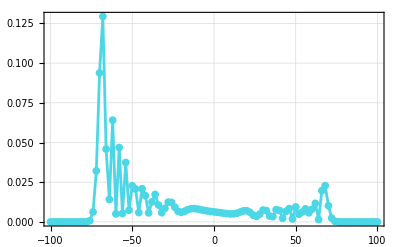

```mathematica
plotminusx0=ListLinePlot[{Range[-100,100,2],probsminusx0[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->AquaC
]
```

### Estado +_y,0

```mathematica
psiplusy0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}]
```

VectorState[{{1/(√2),0,0},{ⅈ/(√2),1,0}}]

```mathematica
rhofplusy0=#.#†&@DTQW2[psiplusy0,100];
```

```mathematica
probsplusy0=Abs@Diagonal@MatrixPartialTrace[rhofplusy0,1,{2,201}];
```

```mathematica
Total@probsplusy0
```

1.

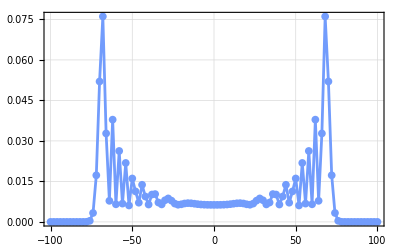

```mathematica
plotplusy0=ListLinePlot[{Range[-100,100,2],probsplusy0[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

### Estado -_y,0

```mathematica
psiminusy0=VectorState[{{1/Sqrt[2],0,0},{-ⅈ/Sqrt[2],1,0}}]
```

VectorState[{{1/(√2),0,0},{-ⅈ/(√2),1,0}}]

```mathematica
rhofminusy0=#.#†&@DTQW2[psiminusy0,100];
```

```mathematica
probsminusy0=Abs@Diagonal@MatrixPartialTrace[rhofminusy0,1,{2,201}];
```

```mathematica
Total@probsminusy0
```

1.

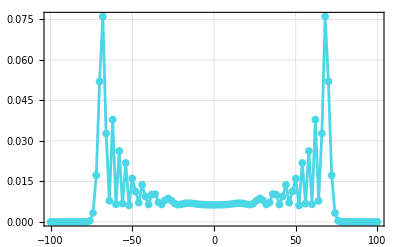

```mathematica
plotminusy0=ListLinePlot[{Range[-100,100,2],probsminusy0[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->AquaC
]
```

### Estado aleatorio puro de la moneda

```mathematica
subs={θ->RandomReal[{0,π}],ϕ->RandomReal[{0,2π}]}
```

{0.599489→0.392286,0.121199→4.41245}

```mathematica
psirandom0=VectorState[{{Cos[θ/2],0,0},{Sin[θ/2]Exp[ⅈ ϕ],1,0}}/.subs]
```

VectorState[{{0.955412,0,0},{0.29311+0.0356997 ⅈ,1,0}}]

```mathematica
rhofrandom0=#.#†&@DTQW2[psirandom0,100];
```

```mathematica
probsrandom0=Abs@Diagonal@MatrixPartialTrace[rhofrandom0,1,{2,201}];
```

```mathematica
Total@probsrandom0
```

1.

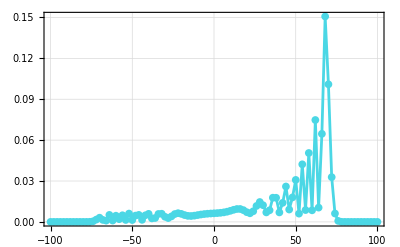

```mathematica
plotrandom0=ListLinePlot[{Range[-100,100,2],probsrandom0[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->AquaC
]
```

### Estado puro superpuestos en la posición 0⊗1/(√2)(10+-10)

```mathematica
psi0superpos10=VectorState[{{1/Sqrt[2],0,10},{1/Sqrt[2],0,-10}}]
```

VectorState[{{1/(√2),0,10},{1/(√2),0,-10}}]

```mathematica
rhof0superpos10=#.#†&@DTQW2[psi0superpos10,100];
```

```mathematica
probs0superpos10=Abs@Diagonal@MatrixPartialTrace[rhof0superpos10,1,{2,201}];
```

```mathematica
Total@probs0superpos10
```

1.

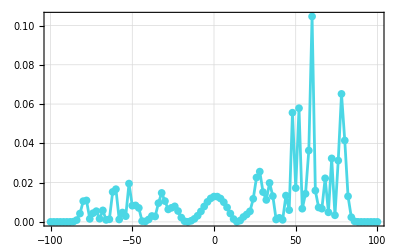

```mathematica
plot0superpos10=ListLinePlot[{Range[-100,100,2],probs0superpos10[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->AquaC
]
```

### Estado puro superpuestos en la moneda y posición 1/(√2)(0+1)⊗1/(√2)(10+-10)

```mathematica
psisuperpos01superpos10=VectorState[{{1/2,0,10},{1/2,0,-10},{1/2,1,10},{1/2,1,-10}}]
```

VectorState[{{1/2,0,10},{1/2,0,-10},{1/2,1,10},{1/2,1,-10}}]

```mathematica
rhofsuperpos01superpos10=#.#†&@DTQW2[psisuperpos01superpos10,100];
```

```mathematica
probssuperpos01superpos10=Abs@Diagonal@MatrixPartialTrace[rhofsuperpos01superpos10,1,{2,201}];
```

```mathematica
Total@probssuperpos01superpos10
```

1.

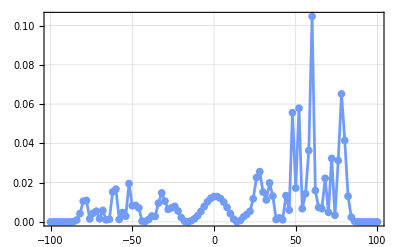

```mathematica
plotsuperpos01superpos10=ListLinePlot[{Range[-100,100,2],probs0superpos10[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

## Estados mixtos de la moneda

Dado un vector de Bloch r⃗=(r_x,r_y,r_z), hallar la matriz de densidad de dicho estado y expresarla como ρ = ∑_i p_i ψ_iψ_i.

```mathematica
FindRhoSumRepresentation[blochVector_]:=1/2(PauliMatrix[0]+blochVector.{PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]})
```

## Estado sobre el eje x

### Primer estado

```mathematica
FindRhoSumRepresentation[{1/5,0,0}]
```

{{1/2,1/10},{1/10,1/2}}

```mathematica
rho1b=DMatrixState[{{1/2,0,0,0,0},{1/10,0,0,1,0},{1/10,1,0,0,0},{1/2,1,0,1,0}}]
```

DMatrixState[{{1/2,0,0,0,0},{1/10,0,0,1,0},{1/10,1,0,0,0},{1/2,1,0,1,0}}]

```mathematica
rhof1b=DTQW2[rho1b,100];
```

```mathematica
probs1b=Abs@Diagonal@MatrixPartialTrace[rhof1b,1,{2,201}];
```

```mathematica
Total@probs1b
```

1.

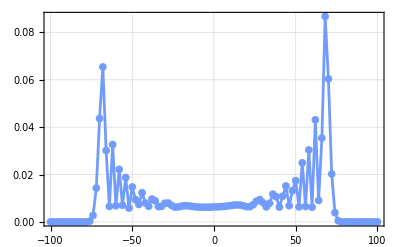

```mathematica
plot1b=ListLinePlot[{Range[-100,100,2],probs1b[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

### Segundo estado

```mathematica
FindRhoSumRepresentation[{-1/5,0,0}]
```

{{1/2,-1/10},{-1/10,1/2}}

```mathematica
rho1d=DMatrixState[{{1/2,0,0,0,0},{-1/10,0,0,1,0},{-1/10,1,0,0,0},{1/2,1,0,1,0}}]
```

DMatrixState[{{1/2,0,0,0,0},{-1/10,0,0,1,0},{-1/10,1,0,0,0},{1/2,1,0,1,0}}]

```mathematica
rhof1d=DTQW2[rho1d,100];
```

```mathematica
probs1d=Abs@Diagonal@MatrixPartialTrace[rhof1d,1,{2,201}];
```

```mathematica
Total@probs1d
```

1.

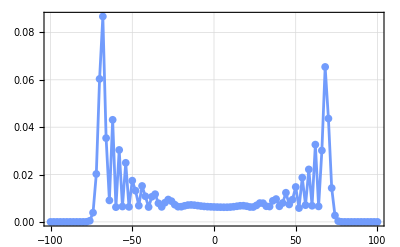

```mathematica
plot1d=ListLinePlot[{Range[-100,100,2],probs1d[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

### Tercer estado

```mathematica
FindRhoSumRepresentation[{4/5,0,0}]
```

{{1/2,2/5},{2/5,1/2}}

```mathematica
rho1a=DMatrixState[{{1/2,0,0,0,0},{2/5,0,0,1,0},{2/5,1,0,0,0},{1/2,1,0,1,0}}]
```

DMatrixState[{{1/2,0,0,0,0},{2/5,0,0,1,0},{2/5,1,0,0,0},{1/2,1,0,1,0}}]

```mathematica
rhof1a=DTQW2[rho1a,100];
```

```mathematica
probs1a=Abs@Diagonal@MatrixPartialTrace[rhof1a,1,{2,201}];
```

```mathematica
Total@probs1a
```

1.

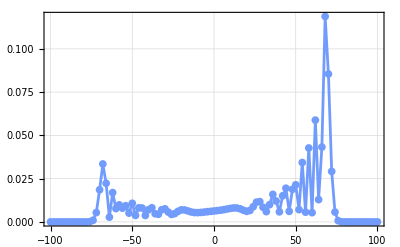

```mathematica
plot1a=ListLinePlot[{Range[-100,100,2],probs1a[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

### Cuarto estado

```mathematica
FindRhoSumRepresentation[{-4/5,0,0}]
```

{{1/2,-2/5},{-2/5,1/2}}

```mathematica
rho1e=DMatrixState[{{1/2,0,0,0,0},{-2/5,0,0,1,0},{-2/5,1,0,0,0},{1/2,1,0,1,0}}]
```

DMatrixState[{{1/2,0,0,0,0},{-2/5,0,0,1,0},{-2/5,1,0,0,0},{1/2,1,0,1,0}}]

```mathematica
rhof1e=DTQW2[rho1e,100];
```

```mathematica
probs1e=Abs@Diagonal@MatrixPartialTrace[rhof1e,1,{2,201}];
```

```mathematica
Total@probs1e
```

1.

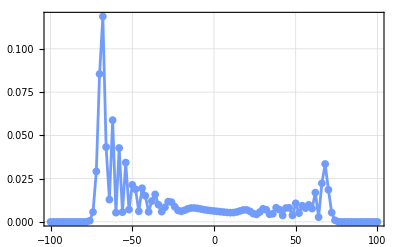

```mathematica
plot1e=ListLinePlot[{Range[-100,100,2],probs1e[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

### Quinto estado

```mathematica
FindRhoSumRepresentation[{1/20,0,0}]
```

{{1/2,1/40},{1/40,1/2}}

```mathematica
rho1c=DMatrixState[{{1/2,0,0,0,0},{1/40,0,0,1,0},{1/40,1,0,0,0},{1/2,1,0,1,0}}]
```

DMatrixState[{{1/2,0,0,0,0},{1/40,0,0,1,0},{1/40,1,0,0,0},{1/2,1,0,1,0}}]

```mathematica
rhof1c=DTQW2[rho1c,100];
```

```mathematica
probs1c=Abs@Diagonal@MatrixPartialTrace[rhof1c,1,{2,201}];
```

```mathematica
Total@probs1c
```

1.

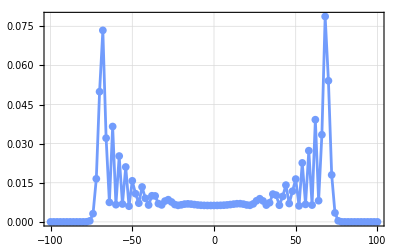

```mathematica
plot1c=ListLinePlot[{Range[-100,100,2],probs1c[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

## Estado sobre el eje y

```mathematica
FindRhoSumRepresentation[{0,1/3,0}]
```

{{1/2,-ⅈ/6},{ⅈ/6,1/2}}

```mathematica
rho2=DMatrixState[{{1/2,0,0,0,0},{-ⅈ/6,0,0,1,0},{ⅈ/6,1,0,0,0},{1/2,1,0,1,0}}]
```

DMatrixState[{{1/2,0,0,0,0},{-ⅈ/6,0,0,1,0},{ⅈ/6,1,0,0,0},{1/2,1,0,1,0}}]

```mathematica
rhof2=DTQW2[rho2,100];
```

```mathematica
probs2=Abs@Diagonal@MatrixPartialTrace[rhof2,1,{2,201}];
```

```mathematica
Total@probs2
```

1.

```mathematica
plot2=ListLinePlot[{Range[-100,100,2],probs2[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

-Graphics-

## Estado sobre el eje z

```mathematica
FindRhoSumRepresentation[{0,0,-1/2}]
```

{{1/4,0},{0,3/4}}

```mathematica
rho3=DMatrixState[{{1/4,0,0,0,0},{3/4,1,0,1,0}}]
```

DMatrixState[{{1/4,0,0,0,0},{3/4,1,0,1,0}}]

```mathematica
rhof3=DTQW2[rho3,100];
```

```mathematica
probs3=Abs@Diagonal@MatrixPartialTrace[rhof3,1,{2,201}];
```

```mathematica
Total@probs3
```

1.

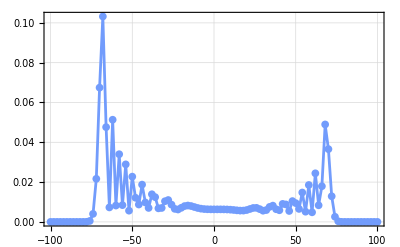

```mathematica
plot3=ListLinePlot[{Range[-100,100,2],probs3[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

## Estado sobre el plano x z

```mathematica
-3/5//N
```

-0.6

```mathematica
-Sqrt[(9/10)^2-(3/5)^2]//N
```

-0.67082

```mathematica
FindRhoSumRepresentation[{-3/5,0,-Sqrt[(9/10)^2-(3/5)^2]}]
```

{{1/2 (1-3/(2 √5)),-3/10},{-3/10,1/2 (1+3/(2 √5))}}

```mathematica
rho4=DMatrixState[{{1/2 (1-3/(2 √5)),0,0,0,0},{-3/10,0,0,1,0},{-3/10,1,0,0,0},{1/2 (1+3/(2 √5)),1,0,1,0}}]
```

DMatrixState[{{1/2 (1-3/(2 √5)),0,0,0,0},{-3/10,0,0,1,0},{-3/10,1,0,0,0},{1/2 (1+3/(2 √5)),1,0,1,0}}]

```mathematica
rhof4=DTQW2[rho4,100];
```

```mathematica
probs4=Abs@Diagonal@MatrixPartialTrace[rhof4,1,{2,201}];
```

```mathematica
Total@probs4
```

1.

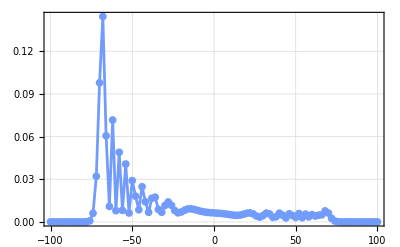

```mathematica
plot4=ListLinePlot[{Range[-100,100,2],probs4[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

## Estado sobre el plano x y

```mathematica
FindRhoSumRepresentation[{-1/2,2/3,0}]
```

{{1/2,-1/4-ⅈ/3},{-1/4+ⅈ/3,1/2}}

```mathematica
rho5=DMatrixState[{{1/2,0,0,0,0},{-1/4-ⅈ/3,0,0,1,0},{-1/4+ⅈ/3,1,0,0,0},{1/2,1,0,1,0}}]
```

DMatrixState[{{1/2,0,0,0,0},{-1/4-ⅈ/3,0,0,1,0},{-1/4+ⅈ/3,1,0,0,0},{1/2,1,0,1,0}}]

```mathematica
rhof5=DTQW2[rho5,100];
```

```mathematica
probs5=Abs@Diagonal@MatrixPartialTrace[rhof5,1,{2,201}];
```

```mathematica
Total@probs5
```

1.

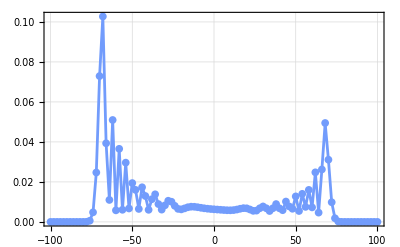

```mathematica
plot5=ListLinePlot[{Range[-100,100,2],probs5[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

## Estado sobre el plano y z

```mathematica
FindRhoSumRepresentation[{0,4/5,1/2}]
```

{{3/4,-(2 ⅈ)/5},{(2 ⅈ)/5,1/4}}

```mathematica
rho6=DMatrixState[{{3/4,0,0,0,0},{-(2 ⅈ)/5,0,0,1,0},{(2 ⅈ)/5,1,0,0,0},{1/4,1,0,1,0}}]
```

DMatrixState[{{3/4,0,0,0,0},{-(2 ⅈ)/5,0,0,1,0},{(2 ⅈ)/5,1,0,0,0},{1/4,1,0,1,0}}]

```mathematica
rhof6=DTQW2[rho6,100];
```

```mathematica
probs6=Abs@Diagonal@MatrixPartialTrace[rhof6,1,{2,201}];
```

```mathematica
Total@probs6
```

1.

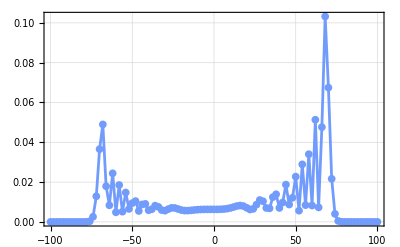

```mathematica
plot6=ListLinePlot[{Range[-100,100,2],probs6[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

## Estado máximamente mixto

```mathematica
FindRhoSumRepresentation[{0,0,0}]
```

{{1/2,0},{0,1/2}}

```mathematica
rho7=DMatrixState[{{1/2,0,0,0,0},{1/2,1,0,1,0}}]
```

DMatrixState[{{1/2,0,0,0,0},{1/2,1,0,1,0}}]

```mathematica
rhof7=DTQW2[rho7,100];
```

```mathematica
probs7=Abs@Diagonal@MatrixPartialTrace[rhof7,1,{2,201}];
```

```mathematica
Total@probs7
```

1.

```mathematica
plot7=ListLinePlot[{Range[-100,100,2],probs7[[;;;;2]]}ᵀ,
plotargs,
PlotRange->All,
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

-Graphics-